# Programa CI 6GDL-ROBOT EN EL ESPACIO MÉTODO MTH^-1, Desacople cinemático y método algebráico

-Graphics-

-Graphics-

Se obtienen las ecuaciones de cinemática directa a partir de la tabla de Denavit-Hartenberg.

## FUNCIONES

```mathematica
(*FUNCIONES DE Matrices de Rotación 3x3 PARA CUALQUIER VARIABLE *)
Rx[α_]:={{1,0,0},{0,Cos[α], -Sin[α]}, {0,Sin[α], Cos[α]}};   
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0}, {-Sin[ϕ],0,Cos[ϕ]}};  
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}};
(*FUNCIONES de Matrices HOMEGENEAS de Traslación y Rotación 4x4 PARA CUALQUIER VARIABLE *)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}

Qx[α_]:={{1,0,0,0},{0,Cos[α], -Sin[α], 0},{0, Sin[α], Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ], 0, Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ], -Sin[θ],0,0},{Sin[θ], Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
(*FUNCIONES de Matrices HOMEGENEAS De Denavit-Hartenberg *)

Q[θ_, d_, a_, α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]

Ma=Q[θ1, d1, a1, α1];
Ma//MatrixForm
(*FUNCIONES ADICIONALES *)
n={0,0,0,1};
T3D[P_]:={P⟦1⟧,P⟦2⟧,P⟦3⟧ }
M3D[Q_]:={{Q⟦1,1⟧,Q⟦1,2⟧, Q⟦1,3⟧ },{Q⟦2,1⟧,Q⟦2,2⟧, Q⟦2,3⟧},{Q⟦3,1⟧,Q⟦3,2⟧, Q⟦3,3⟧}}
T={{Nx, Ox, Ax,x},{Ny, Oy, Ay,y},{Nz, Oz, Az,z},{0,0,0,1}};
(*MAtriz de punto medio*)
Tm={{NXm, OXm, AXm,xm},{NYm, OYm, AYm,ym},{NZm, OZm, AZm,zm},{0,0,0,1}};
T//MatrixForm
(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

(Cos[θ1] | -Cos[α1] Sin[θ1] | Sin[α1] Sin[θ1] | a1 Cos[θ1]
Sin[θ1] | Cos[α1] Cos[θ1] | -Cos[θ1] Sin[α1] | a1 Sin[θ1]
0 | Sin[α1] | Cos[α1] | d1
0 | 0 | 0 | 1)

(Nx | Ox | Ax | x
Ny | Oy | Ay | y
Nz | Oz | Az | z
0 | 0 | 0 | 1)

## CINEMÁTICA DIRECTA 3 GDL DENAVIT-HARTENBERG

-Graphics-

## DH 14- OBTENER LAS MATRICES ^(i-1)A_i

```mathematica
Underoverscript[a, 1, 0]=Q[θ1,ℓ1,0,90°];
Underoverscript[a, 2, 1]=Q[θ2, 0,ℓ2,0];
Underoverscript[a, 3, 2]=Q[90°+θ3, 0,0,90°];
Underoverscript[a, 4, 3]=Q[θ4, ℓ3+ℓ4,0,-90°];
Underoverscript[a, 5, 4]=Q[θ5, 0,0,90°];
Underoverscript[a, 6, 5]=Q[θ6, ℓ5+ℓ6,0,0];
```

## DH 15- OBTENER LAS MATRICES ^0 A_6=^0 A_1.^1 A_2.^2 A_3.....

```mathematica
Underoverscript[a, 2, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1]//Simplify;
Underoverscript[a, 3, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2]//Simplify;
Underoverscript[a, 4, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3]//Simplify;
Underoverscript[a, 5, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3].Underoverscript[a, 5, 4]//Simplify;
Underoverscript[a, 6, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3].Underoverscript[a, 5, 4].Underoverscript[a, 6, 5]//Simplify;
Underoverscript[a, 6, 0].n//MatrixForm
```

(ℓ2 Cos[θ1] Cos[θ2]+(ℓ3+ℓ4) Cos[θ1] Cos[θ2+θ3]+(ℓ5+ℓ6) (Sin[θ1] Sin[θ4] Sin[θ5]-Cos[θ1] (Sin[θ2] (Cos[θ5] Sin[θ3]+Cos[θ3] Cos[θ4] Sin[θ5])+Cos[θ2] (-Cos[θ3] Cos[θ5]+Cos[θ4] Sin[θ3] Sin[θ5])))
ℓ2 Cos[θ2] Sin[θ1]+(ℓ3+ℓ4) Cos[θ2+θ3] Sin[θ1]-(ℓ5+ℓ6) (Cos[θ5] Sin[θ1] Sin[θ2] Sin[θ3]+(Cos[θ3] Cos[θ4] Sin[θ1] Sin[θ2]+Cos[θ1] Sin[θ4]) Sin[θ5]+Cos[θ2] Sin[θ1] (-Cos[θ3] Cos[θ5]+Cos[θ4] Sin[θ3] Sin[θ5]))
ℓ1+ℓ2 Sin[θ2]+(ℓ3+ℓ4) Sin[θ2+θ3]+(ℓ5+ℓ6) (Cos[θ3] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ5]-Cos[θ4] Sin[θ2] Sin[θ5]))
1)

## DH 16- Vector de Posición del Efector Final y SubMatriz de Orientación

### Vector de Posición

```mathematica
X=Underoverscript[a, 6, 0]⟦1,4⟧//Simplify
Y=Underoverscript[a, 6, 0]⟦2,4⟧//Simplify
Z=Underoverscript[a, 6, 0]⟦3,4⟧//Simplify
```

ℓ2 Cos[θ1] Cos[θ2]+(ℓ3+ℓ4) Cos[θ1] Cos[θ2+θ3]+(ℓ5+ℓ6) (Sin[θ1] Sin[θ4] Sin[θ5]-Cos[θ1] (Sin[θ2] (Cos[θ5] Sin[θ3]+Cos[θ3] Cos[θ4] Sin[θ5])+Cos[θ2] (-Cos[θ3] Cos[θ5]+Cos[θ4] Sin[θ3] Sin[θ5])))

ℓ2 Cos[θ2] Sin[θ1]+(ℓ3+ℓ4) Cos[θ2+θ3] Sin[θ1]-(ℓ5+ℓ6) (Cos[θ5] Sin[θ1] Sin[θ2] Sin[θ3]+(Cos[θ3] Cos[θ4] Sin[θ1] Sin[θ2]+Cos[θ1] Sin[θ4]) Sin[θ5]+Cos[θ2] Sin[θ1] (-Cos[θ3] Cos[θ5]+Cos[θ4] Sin[θ3] Sin[θ5]))

ℓ1+ℓ2 Sin[θ2]+(ℓ3+ℓ4) Sin[θ2+θ3]+(ℓ5+ℓ6) (Cos[θ3] (Cos[θ5] Sin[θ2]+Cos[θ2] Cos[θ4] Sin[θ5])+Sin[θ3] (Cos[θ2] Cos[θ5]-Cos[θ4] Sin[θ2] Sin[θ5]))

### SubMatriz de Rotación

```mathematica
NX=Underoverscript[a, 6, 0]⟦1,1⟧//FullSimplify;
OX=Underoverscript[a, 6, 0]⟦1,2⟧//FullSimplify;
AX=Underoverscript[a, 6, 0]⟦1,3⟧//FullSimplify;

NY=Underoverscript[a, 6, 0]⟦2,1⟧//FullSimplify;
OY=Underoverscript[a, 6, 0]⟦2,2⟧//FullSimplify;
AY=Underoverscript[a, 6, 0]⟦2,3⟧//FullSimplify;

NZ=Underoverscript[a, 6, 0]⟦3,1⟧//FullSimplify;
OZ=Underoverscript[a, 6, 0]⟦3,2⟧//FullSimplify;
AZ=Underoverscript[a, 6, 0]⟦3,3⟧//FullSimplify;
```

## CINEMÁTICA INVERSA POR MÉTODO ALGEBRAICO

## DESACOPLE CINEMÁTICO

Se divide en dos partes al manipulador para las ecuaciones de posición. Se toman dos casos:
	a) La matriz de a_3^0.n----->a_6^0.n=a_3^0.n.a_6^3.n, Se debe encontrar a θ1, θ2, θ3
	b) La matriz de a_4^0.n----->a_6^0.n=a_4^0.n.a_6^4.n, Se debe encontrar a θ1, θ2, θ3

## MATRIZ DE POSICIÓN

```mathematica
Underoverscript[a, 3, 0].n//MatrixForm
```

```mathematica
Underoverscript[a, 3, 0].n
```

{ℓ2 Cos[θ1] Cos[θ2],ℓ2 Cos[θ2] Sin[θ1],ℓ1+ℓ2 Sin[θ2],1}

Vemos que no hay θ3 aquí debido a las juntas y cómo se mueven, los ejes de las juntas 3 y 4 se cortan en θ3, por lo que el sist. 4 queda en θ3

```mathematica
Underoverscript[a, 4, 0].n//MatrixForm
```

```mathematica
Underoverscript[a, 4, 0].n
```

{Cos[θ1] (ℓ2 Cos[θ2]+(ℓ3+ℓ4) Cos[θ2+θ3]),(ℓ2 Cos[θ2]+(ℓ3+ℓ4) Cos[θ2+θ3]) Sin[θ1],ℓ1+ℓ2 Sin[θ2]+(ℓ3+ℓ4) Sin[θ2+θ3],1}

Ahora necesitamos la otra parte, la de 6 en 4

```mathematica
Underoverscript[a, 6, 4]=Underoverscript[a, 5, 4].Underoverscript[a, 6, 5]//Simplify;
Underoverscript[a, 6, 4].n//MatrixForm
```

```mathematica
Underoverscript[a, 5, 4].Underoverscript[a, 6, 5].n
```

{(ℓ5+ℓ6) Sin[θ5],-(ℓ5+ℓ6) Cos[θ5],0,1}

Hacemos un cambio de variable, considerando que el efector es colinear a los eslabones 5 y 6. eso hace que nuestro vector a sea paralelo a l5 y l6, por lo que el cambio de variable es posible.

```mathematica
-Graphics-
-Graphics-
```

-Graphics-

-Graphics-

### Solución THETA 1

```mathematica
t1=ArcTan[x,y]
```

ArcTan[x,y]

### SOLUCIÓN THETA3

Solución de la cinemática por MTH^-1
a_4^0=a_1^0.a_2^1.a_3^2.a_4^3

(a_1^0)^-1 =a_0^1

(a_1^0)^-1 a_4^0=(a_1^0)^-1 .a_1^0.a_2^1.a_3^2.a_4^3 → 
(a_2^1)^-1(a_3^2)^-1(a_4^3)^-1

```mathematica
Underoverscript[aDn, 4, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3].n;
Underoverscript[aD, 4, 0]//MatrixForm;
Underoverscript[aIn, 4, 0]=Tm.n
Underoverscript[a, 0, 1]=Inverse[Underoverscript[a, 1, 0]];
Underoverscript[aDnxI, 4, 0]=Underoverscript[a, 0, 1].Underoverscript[a, 1, 0].Underoverscript[a, 2, 1].Underoverscript[a, 3, 2].Underoverscript[a, 4, 3].n//Simplify;
Underoverscript[aDnxI, 4, 0]//MatrixForm
Underoverscript[aInxI, 4, 0]=Underoverscript[a, 0, 1].Tm.n//Simplify;
Underoverscript[aInxI, 4, 0]//MatrixForm
```

{xm,ym,zm,1}

(ℓ2 Cos[θ2]+(ℓ3+ℓ4) Cos[θ2+θ3]
ℓ2 Sin[θ2]+(ℓ3+ℓ4) Sin[θ2+θ3]
0
1)

(xm Cos[θ1]+ym Sin[θ1]
zm-ℓ1
-ym Cos[θ1]+xm Sin[θ1]
1)

#### Elementos de la matriz MTH con a_0^2

```mathematica
Underoverscript[a, 0, 2]=Inverse[Underoverscript[a, 1, 0].Underoverscript[a, 2, 1]];
Underoverscript[aDn, 4, 2]=Underoverscript[a, 0, 2].Underoverscript[aDn, 4, 0]//Simplify;
Underoverscript[aDn, 4, 2]//MatrixForm 
Underoverscript[aIn, 4, 2]=Underoverscript[a, 0, 2].Underoverscript[aIn, 4, 0]//Simplify;
Underoverscript[aIn, 4, 2]//MatrixForm
```

((ℓ3+ℓ4) Cos[θ3]
(ℓ3+ℓ4) Sin[θ3]
0
1)

(-ℓ2+xm Cos[θ1] Cos[θ2]+ym Cos[θ2] Sin[θ1]+zm Sin[θ2]-ℓ1 Sin[θ2]
(zm-ℓ1) Cos[θ2]-(xm Cos[θ1]+ym Sin[θ1]) Sin[θ2]
-ym Cos[θ1]+xm Sin[θ1]
1)

```mathematica
Underoverscript[XD, 4, 2]=Underoverscript[aDn, 4, 2]⟦1⟧+ℓ2;
Underoverscript[YD, 4, 2]=Underoverscript[aDn, 4, 2]⟦2⟧;
Underoverscript[ZD, 4, 2]=Underoverscript[aDn, 4, 2]⟦3⟧;
Underoverscript[XI, 4, 2]=Underoverscript[aIn, 4, 2]⟦1⟧+ℓ2;
Underoverscript[YI, 4, 2]=Underoverscript[aIn, 4, 2]⟦2⟧;
Underoverscript[ZI, 4, 2]=Underoverscript[aIn, 4, 2]⟦3⟧;
Underoverscript[SLDXY2, 4, 2]=Underoverscript[XD, 4, 2]^2+Underoverscript[YD, 4, 2]^2//FullSimplify
Underoverscript[SLIXY2, 4, 2]=Underoverscript[XI, 4, 2]^2+Underoverscript[YI, 4, 2]^2//FullSimplify
```

ℓ2^2+(ℓ3+ℓ4) (ℓ3+ℓ4+2 ℓ2 Cos[θ3])

(zm-ℓ1)^2+(xm Cos[θ1]+ym Sin[θ1])^2

```mathematica
SolC3=Solve[Underoverscript[SLDXY2, 4, 2]==Underoverscript[SLIXY2, 4, 2], Cos[θ3]]//Flatten//FullSimplify;
C3=Cos[θ3]/.SolC3;
S3=√(1-C3^2);
t3=ArcTan[C3,S3]/.xm-> x-(ℓ5+ℓ6)*Ax/.ym-> y+(ℓ5+ℓ6)*Ay/.zm-> z-(ℓ5+ℓ6)*Az (*CAMBIO DE VARIABLE*)
```

ArcTan[1/(2 ℓ2 (ℓ3+ℓ4))(-ℓ2^2-(ℓ3+ℓ4)^2+(z-ℓ1-Az (ℓ5+ℓ6))^2+((x-Ax (ℓ5+ℓ6)) Cos[θ1]+(y+Ay (ℓ5+ℓ6)) Sin[θ1])^2),√(1-1/(4 ℓ2^2 (ℓ3+ℓ4)^2)(-ℓ2^2-(ℓ3+ℓ4)^2+(z-ℓ1-Az (ℓ5+ℓ6))^2+((x-Ax (ℓ5+ℓ6)) Cos[θ1]+(y+Ay (ℓ5+ℓ6)) Sin[θ1])^2)^2)]

### Solución theta 2

```mathematica
Underoverscript[XDe, 4, 2]=Underoverscript[XD, 4, 2]//TrigExpand;
Underoverscript[YDe, 4, 2]=Underoverscript[YD, 4, 2]//TrigExpand;
Underoverscript[ZDe, 4, 2]=Underoverscript[ZD, 4, 2]//TrigExpand;
Underoverscript[XIe, 4, 2]=Underoverscript[XI, 4, 2]//TrigExpand;
Underoverscript[YIe, 4, 2]=Underoverscript[YI, 4, 2]//TrigExpand;
Underoverscript[ZIe, 4, 2]=Underoverscript[ZI, 4, 2]//TrigExpand;
```

```mathematica
SolC2S2=Solve[{Underoverscript[XDe, 4, 2]==Underoverscript[XIe, 4, 2],Underoverscript[YDe, 4, 2]==Underoverscript[YIe, 4, 2]},{Cos[θ2],Sin[θ2]}]//Flatten//Simplify;
```

```mathematica
(*SE TOMAN 2 ECUACIONES X,Y Y DOS INCOGNITAS COS[θ2],SIN[θ2]*)
```

```mathematica
C2=Cos[θ2]/.SolC2S2⟦1⟧;
S2=Sin[θ2]/.SolC2S2⟦2⟧;
t2=ArcTan[C2,S2]/.xm-> x-(ℓ5+ℓ6)*Ax/.ym-> y+(ℓ5+ℓ6)*Ay/.zm-> z-(ℓ5+ℓ6)*Az (*CAMBIO DE VARIABLE*)
```

ArcTan[((x-Ax (ℓ5+ℓ6)) Cos[θ1] (ℓ2+(ℓ3+ℓ4) Cos[θ3])+(y+Ay (ℓ5+ℓ6)) (ℓ2+(ℓ3+ℓ4) Cos[θ3]) Sin[θ1]+(ℓ3+ℓ4) (z-ℓ1-Az (ℓ5+ℓ6)) Sin[θ3])/(ℓ1^2-2 ℓ1 (z-Az (ℓ5+ℓ6))+(z-Az (ℓ5+ℓ6))^2+(x-Ax (ℓ5+ℓ6))^2 Cos[θ1]^2+(y+Ay (ℓ5+ℓ6))^2 Sin[θ1]^2+(x-Ax (ℓ5+ℓ6)) (y+Ay (ℓ5+ℓ6)) Sin[2 θ1]),-((ℓ1 ℓ2-ℓ2 (z-Az (ℓ5+ℓ6))-(ℓ3+ℓ4) (z-ℓ1-Az (ℓ5+ℓ6)) Cos[θ3]+(ℓ3+ℓ4) (x-Ax (ℓ5+ℓ6)) Cos[θ1] Sin[θ3]+ℓ3 (y+Ay (ℓ5+ℓ6)) Sin[θ1] Sin[θ3]+ℓ4 (y+Ay (ℓ5+ℓ6)) Sin[θ1] Sin[θ3])/(ℓ1^2-2 ℓ1 (z-Az (ℓ5+ℓ6))+(z-Az (ℓ5+ℓ6))^2+(x-Ax (ℓ5+ℓ6))^2 Cos[θ1]^2+(y+Ay (ℓ5+ℓ6))^2 Sin[θ1]^2+(x-Ax (ℓ5+ℓ6)) (y+Ay (ℓ5+ℓ6)) Sin[2 θ1]))]

## ORIENTACIÓN DEL EFECTOR FINAL

```mathematica
Underoverscript[RD, 3, 0]=M3D[Underoverscript[a, 3, 0]]; (*ES LA NOA*)
Underoverscript[RD, 3, 0]//MatrixForm
Underoverscript[a, 6, 3]=Underoverscript[a, 4, 3].Underoverscript[a, 5, 4].Underoverscript[a, 6, 5]//Simplify;
Underoverscript[RD, 6, 3]=M3D[Underoverscript[a, 6, 3]]//FullSimplify; (*ES LA NOA*)
Underoverscript[RD, 6, 3]//MatrixForm
```

(-Cos[θ1] Sin[θ2+θ3] | Sin[θ1] | Cos[θ1] Cos[θ2+θ3]
-Sin[θ1] Sin[θ2+θ3] | -Cos[θ1] | Cos[θ2+θ3] Sin[θ1]
Cos[θ2+θ3] | 0 | Sin[θ2+θ3])

(Cos[θ4] Cos[θ5] Cos[θ6]-Sin[θ4] Sin[θ6] | -Cos[θ6] Sin[θ4]-Cos[θ4] Cos[θ5] Sin[θ6] | Cos[θ4] Sin[θ5]
Cos[θ5] Cos[θ6] Sin[θ4]+Cos[θ4] Sin[θ6] | Cos[θ4] Cos[θ6]-Cos[θ5] Sin[θ4] Sin[θ6] | Sin[θ4] Sin[θ5]
-Cos[θ6] Sin[θ5] | Sin[θ5] Sin[θ6] | Cos[θ5])

```mathematica
Underoverscript[RI, 6, 0]=M3D[T];
Underoverscript[RI, 6, 0]//MatrixForm;
Underoverscript[R, 0, 3]=Inverse[Underoverscript[RD, 3, 0]];
Underoverscript[RI, 6, 3]=Underoverscript[R, 0, 3].Underoverscript[RI, 6, 0]//Simplify;
Underoverscript[RI, 6, 3]//MatrixForm
Underoverscript[RD, 6, 3]//MatrixForm
```

(Nz Cos[θ1]^2 Cos[θ2+θ3]-Nx Cos[θ1] Sin[θ2+θ3]+Sin[θ1] (Nz Cos[θ2+θ3] Sin[θ1]-Ny Sin[θ2+θ3]) | Oz Cos[θ1]^2 Cos[θ2+θ3]-Ox Cos[θ1] Sin[θ2+θ3]+Sin[θ1] (Oz Cos[θ2+θ3] Sin[θ1]-Oy Sin[θ2+θ3]) | Az Cos[θ1]^2 Cos[θ2+θ3]-Ax Cos[θ1] Sin[θ2+θ3]+Sin[θ1] (Az Cos[θ2+θ3] Sin[θ1]-Ay Sin[θ2+θ3])
-Ny Cos[θ1]+Nx Sin[θ1] | -Oy Cos[θ1]+Ox Sin[θ1] | -Ay Cos[θ1]+Ax Sin[θ1]
Nx Cos[θ1] Cos[θ2+θ3]+Nz Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Ny Cos[θ2+θ3]+Nz Sin[θ1] Sin[θ2+θ3]) | Ox Cos[θ1] Cos[θ2+θ3]+Oz Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Oy Cos[θ2+θ3]+Oz Sin[θ1] Sin[θ2+θ3]) | Ax Cos[θ1] Cos[θ2+θ3]+Az Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Ay Cos[θ2+θ3]+Az Sin[θ1] Sin[θ2+θ3]))

(Cos[θ4] Cos[θ5] Cos[θ6]-Sin[θ4] Sin[θ6] | -Cos[θ6] Sin[θ4]-Cos[θ4] Cos[θ5] Sin[θ6] | Cos[θ4] Sin[θ5]
Cos[θ5] Cos[θ6] Sin[θ4]+Cos[θ4] Sin[θ6] | Cos[θ4] Cos[θ6]-Cos[θ5] Sin[θ4] Sin[θ6] | Sin[θ4] Sin[θ5]
-Cos[θ6] Sin[θ5] | Sin[θ5] Sin[θ6] | Cos[θ5])

## theta 5

```mathematica
C5D=Underoverscript[RD, 6, 3]⟦3,3⟧;
C5I=Underoverscript[RI, 6, 3]⟦3,3⟧;
C5=C5I;
S5=√(1-C5^2);
t5=ArcTan[C5,S5]
```

ArcTan[Ax Cos[θ1] Cos[θ2+θ3]+Az Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Ay Cos[θ2+θ3]+Az Sin[θ1] Sin[θ2+θ3]),√(1-(Ax Cos[θ1] Cos[θ2+θ3]+Az Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Ay Cos[θ2+θ3]+Az Sin[θ1] Sin[θ2+θ3]))^2)]

## theta 4

```mathematica
C4D=Underoverscript[RD, 6, 3]⟦1,3⟧;
S4D=Underoverscript[RD, 6, 3]⟦2,3⟧;
S4D/C4D;

C4I=Underoverscript[RI, 6, 3]⟦1,3⟧;
S4I=Underoverscript[RI, 6, 3]⟦2,3⟧;
t4=ArcTan[C4I,S4I]
```

ArcTan[Az Cos[θ1]^2 Cos[θ2+θ3]-Ax Cos[θ1] Sin[θ2+θ3]+Sin[θ1] (Az Cos[θ2+θ3] Sin[θ1]-Ay Sin[θ2+θ3]),-Ay Cos[θ1]+Ax Sin[θ1]]

## theta 6

```mathematica
C6D=Underoverscript[RD, 6, 3]⟦3,1⟧*-1;
S6D=Underoverscript[RD, 6, 3]⟦3,2⟧;
S6D/C6D;

C6I=Underoverscript[RI, 6, 3]⟦3,1⟧*-1;
S6I=Underoverscript[RI, 6, 3]⟦3,2⟧;
t6=ArcTan[C6I,S6I]
```

ArcTan[-Nx Cos[θ1] Cos[θ2+θ3]-Nz Cos[θ1]^2 Sin[θ2+θ3]-Sin[θ1] (Ny Cos[θ2+θ3]+Nz Sin[θ1] Sin[θ2+θ3]),Ox Cos[θ1] Cos[θ2+θ3]+Oz Cos[θ1]^2 Sin[θ2+θ3]+Sin[θ1] (Oy Cos[θ2+θ3]+Oz Sin[θ1] Sin[θ2+θ3])]

## DATOS

```mathematica
ℓ1=50;
ℓ2=60;
ℓ3=50;
ℓ4=20;
ℓ5=60;
ℓ6=20;
Nx=-1; Ny=0; Nz=0;
Ox=0; Oy=1; Oz=0;
Ax=0;Ay=0; Az=-1;
```

## TRAYECTORIA

```mathematica
tf=100;
aa=5;
Cero={0,0,0};
For[t=0, t≤tf, t+=1,
Perfil=10*(t/tf)^3-15*(t/tf)^4 +6*(t/tf)^5;

Trayectoria[t]={
2*aa*Cos[2*Pi*Perfil]-aa*Cos[4*Pi*Perfil]+10,
2*aa*Sin[4*Pi*Perfil]-aa*Sin[4*Pi*Perfil]+20,
2*aa*Sin[4*Pi*Perfil]-aa*Sin[4*Pi*Perfil]+80
};
];
Tablaxyz=Table[{Trayectoria[t]⟦1⟧,Trayectoria[t]⟦2⟧,Trayectoria[t]⟦3⟧},{t,0,tf,1}];
TrayectoriaEF=Line[Tablaxyz];
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-100,300}, {-100,300},{-100,300}}
]
```

-Graphics3D-

## VALORES DE LAS VARIABLES ARTICULARES EN CINEMÁTICA INVERSA

```mathematica
For[t=0, t≤ tf, t+=1,
x=Trayectoria[t]⟦1⟧;
y=Trayectoria[t]⟦2⟧;
z=Trayectoria[t]⟦3⟧;

θ1a[t]=t1;
θ1=θ1a[t];

θ3a[t]=t3;
θ3=θ3a[t];

θ2a[t]=t2;
θ2=θ2a[t];

θ5a[t]=t5;
θ5=θ5a[t];

θ4a[t]=t4;
θ4=θ4a[t];

θ6a[t]=t6;
θ6=θ6a[t];
]
θ1a[5]//N
θ2a[5]//N
θ3a[5]//N
θ4a[5]//N
θ5a[5]//N
θ6a[5]//N
```

0.929029

0.782311

1.04115

0.

2.88893

-2.21256

## SIMULACIÓN

```mathematica
Animate[
θ1=θ1a[t];
θ3=θ3a[t];
θ2=θ2a[t];
θ4=θ4a[t];
θ5=θ5a[t];
θ6=θ6a[t];

Eslabon1=Line[{Cero,T3D[Underoverscript[a, 1, 0].n]}];
Eslabon2=Line[{T3D[Underoverscript[a, 1, 0].n],T3D[Underoverscript[a, 2, 0].n]}];
Eslabon3=Line[{T3D[Underoverscript[a, 2, 0].n],T3D[Underoverscript[a, 3, 0].n]}];

Eslabon4=Line[{T3D[Underoverscript[a, 3, 0].n],T3D[Underoverscript[a, 4, 0].n]}];
Eslabon5=Line[{T3D[Underoverscript[a, 4, 0].n],T3D[Underoverscript[a, 5, 0].n]}];
Eslabon6=Line[{T3D[Underoverscript[a, 5, 0].n],T3D[Underoverscript[a, 6, 0].n]}];
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon1}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon2},
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon3},
{AbsoluteThickness[5],RGBColor[1,0,0],Eslabon4}, 
{AbsoluteThickness[4],RGBColor[0,.7,0],Eslabon5},
{AbsoluteThickness[4],RGBColor[0,0,1],Eslabon6}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-100,200}, {-100,200},{-100,200}}
],{t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

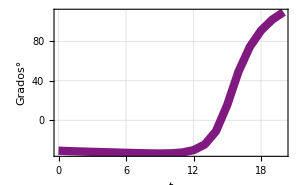

```mathematica
Tabla1=Table[{t, (θ1/.VartArt[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

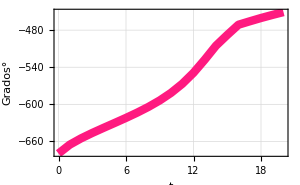

```mathematica
Tabla2=Table[{t, (θ2/.VartArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,1,.1,.5,"t", "Grados°"]
```

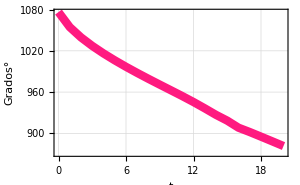

```mathematica
Tabla3=Table[{t, (θ3/.VartArt[t])/Degree},{t,0,tf,1}];
Theta3=Grafica[Tabla3,1,.1,.5,"t", "Grados°"]
```

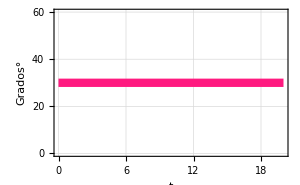

```mathematica
Tabla4=Table[{t, (θ4/.VartArt[t])/Degree},{t,0,tf,1}];
Theta4=Grafica[Tabla4,1,.1,.5,"t", "Grados°"]
```

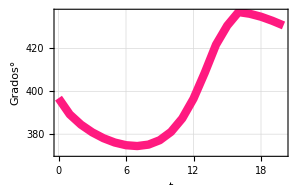

```mathematica
Tabla5=Table[{t, (θ5/.VartArt[t])/Degree},{t,0,tf,1}];
Theta5=Grafica[Tabla5,1,.1,.5,"t", "Grados°"]
```

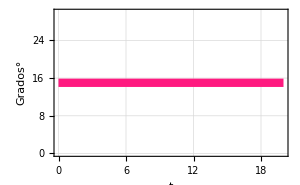

```mathematica
Tabla6=Table[{t, (θ6/.VartArt[t])/Degree},{t,0,tf,1}];
Theta6=Grafica[Tabla6,1,.1,.5,"t", "Grados°"]
```